Global Variables

```mathematica
prec=100;

Nmax = 100;

x1 = 1.0;
x2 = 10.0;
x3 = 20.0;

xmax = 20.0;
xmin = -20.0;
xsize = 100;
dx=(xmax-xmin)/(xsize-1);

Xvector = N[Range[xmin,xmax,dx],prec];
Nvector = Range[0,Nmax,1];
```

Wavefuntion_Wolfram_Mathematica_1

```mathematica
WavefunctionMathematica1[n_,x_,prec_]:=Module[{nPrec,xPrec,norm,H,wavefunction},
SetPrecision[n,prec];
SetPrecision[x,prec];
norm=(2^(-0.5*n))*(Gamma[n+1]^(-0.5))*(Pi^(-0.25));
H=HermiteH[n,x];
wavefunction=SetPrecision[norm*Exp[-0.5*x^2]*H,prec];
wavefunction];
```

Wavefuntion_Wolfram_Mathematica_2

```mathematica
WavefunctionMathematica2[n_,x_,prec_]:=Module[{wavefunction,xsize,i},SetPrecision[x,prec];
wavefunction=Table[SetPrecision[0,prec],{n+1},{Length[x]}];
wavefunction[[1]]=SetPrecision[Pi^(-1/4) Exp[-(x^2)/2],prec];
wavefunction[[2]]=SetPrecision[(2 x wavefunction[[1]])/Sqrt[2],prec];
For[i=3,i<=n+1,i++,wavefunction[[i]]=2 x (wavefunction[[i-1]]/Sqrt[2 (i-1)])-Sqrt[(i-2)/(i-1)] wavefunction[[i-2]];];
wavefunction[[n+1]]];
```

Wavefuntion_Wolfram_Mathematica_3

```mathematica
WavefunctionMathematica3[n_,x_,prec_]:=Module[{wavefunction,i},SetPrecision[x,prec];
wavefunction=Table[SetPrecision[0,prec],{n+1},{Length[x]}];
wavefunction[[1]]=SetPrecision[Pi^(-1/4) Exp[-(x^2)/2],prec];
For[i=1,i<=n,i++,
wavefunction[[i+1]]=
SetPrecision[2 x (wavefunction[[i]]/Sqrt[2 (i)])-Sqrt[(i-1)/i] wavefunction[[i-1]],prec]];
wavefunction];
```

#### Single Fock and Single Position Function with x = 1.0

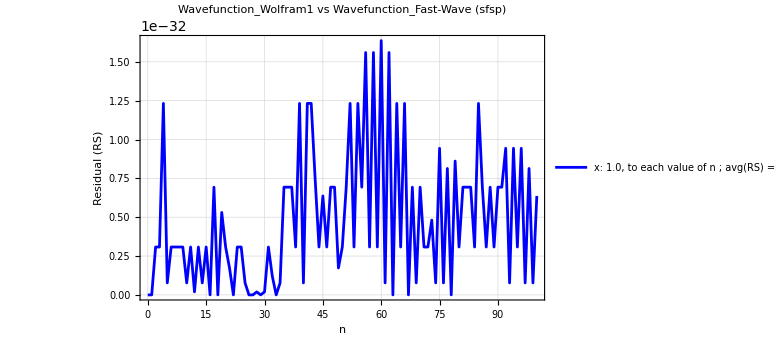

```mathematica
FastWaveSFSpN100x1=SetPrecision[Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_cython as wc;import numpy as np;N_max = 100;x1 = 1.0;np.array([wc.psi_n_single_fock_single_position(n,x1) for n in range(N_max+1)]);"]],prec];

(*WolframSFSpN100x1 = WavefunctionMathematica3[Nmax,x1,prec];*)
WolframSFSpN100x1 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSFSpN100x1,WavefunctionMathematica1[i-1,x1,prec]];]

Residual = (WolframSFSpN100x1-FastWaveSFSpN100x1)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave (sfsp)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{"x: 1.0, to each value of n ; \n avg(RS) = " <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]},Below],
ImageSize->Large
 ]
```

#### Single Fock and Single Position Function with x = 10.0

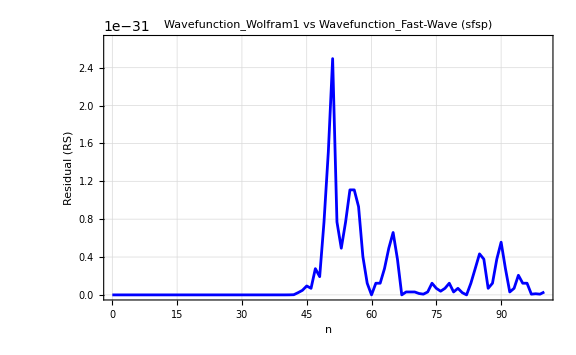

```mathematica
FastWaveSFSpN100x2=SetPrecision[Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_cython as wc;import numpy as np;N_max = 100;x2 = 10.0;np.array([wc.psi_n_single_fock_single_position(n,x2) for n in range(N_max+1)]);"]],prec];

(*WolframSFSpN100x2 = WavefunctionMathematica3[Nmax,x2,prec];*)

WolframSFSpN100x2 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSFSpN100x2,WavefunctionMathematica1[i-1,x2,prec]];]

Residual = (WolframSFSpN100x2-FastWaveSFSpN100x2)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave (sfsp)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 10.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-30.65)}}
]
```

#### Single Fock and Single Position Function with x = 20.0

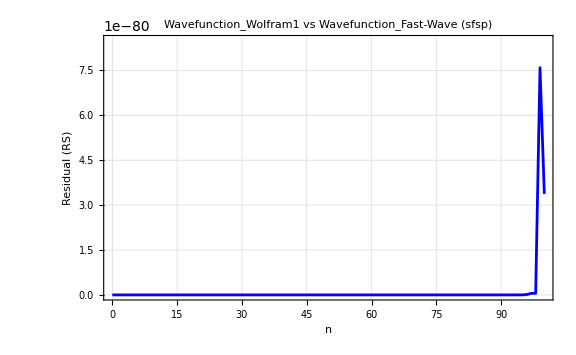

```mathematica
FastWaveSFSpN100x3=SetPrecision[Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_cython as wc;import numpy as np;N_max = 100;x3 = 20.0;np.array([wc.psi_n_single_fock_single_position(n,x3) for n in range(N_max+1)]);"]],prec];

(*WolframSFSpN100x3 = WavefunctionMathematica3[Nmax,x3,prec];*)
WolframSFSpN100x3 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSFSpN100x3,WavefunctionMathematica1[i-1,x3,prec]];]

Residual =( WolframSFSpN100x3-FastWaveSFSpN100x3)^2;


ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave (sfsp)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 20.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-79.15)}}
]
```

#### Single Fock and Multiple Position Function with X = [(-20) → 20; 100]

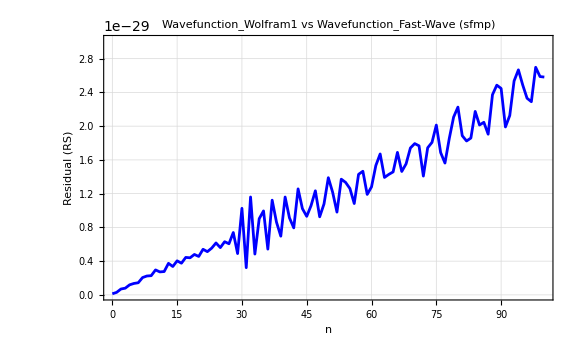

```mathematica
FastWaveSFMpN100X=SetPrecision[Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_cython as wc;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);np.array([wc.psi_n_single_fock_multiple_position(n,X) for n in range(N_max+1)]);"]],prec];

(*WolframSFMpN100X = WavefunctionMathematica3[Nmax,Xvector,prec];*)
WolframSFMpN100X = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframSFMpN100X,WavefunctionMathematica1[i-1,Xvector,prec]];]


ResidualMatrix =(WolframSFMpN100X - FastWaveSFMpN100X)^2;

Residual = Mean /@ResidualMatrix;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram1 vs Wavefunction_Fast-Wave (sfmp)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" X: [(-20)→20;100], to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large,
PlotRange->{{Automatic,Automatic},{0,1.2*10^(-28.6)}}
 ]
```

#### Multiple Fock and Single Position Function with x = 1.0

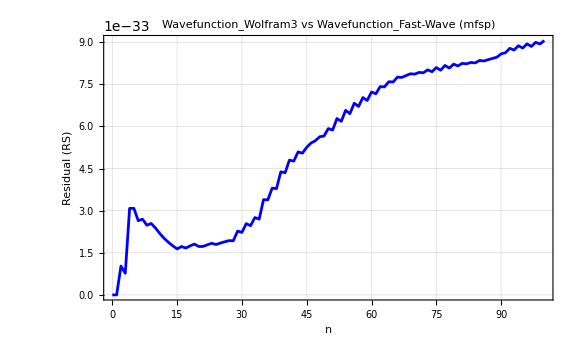

```mathematica
FastWaveMFSpN100x1=SetPrecision[Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_cython as wc;import numpy as np;N_max = 100;x1 =1.0;[wc.psi_n_multiple_fock_single_position(n,x1) for n in range(N_max+1)];"]],prec];

WavefunctionMFSpN100x1 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionMFSpN100x1 ,WavefunctionMathematica3[i-1,x1,prec]];]
ResidualList = (WavefunctionMFSpN100x1 - FastWaveMFSpN100x1)^2;

Residual = Mean /@ResidualList;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave (mfsp)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 1.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ]
```

#### Multiple Fock and Single Position Function with x = 10.0

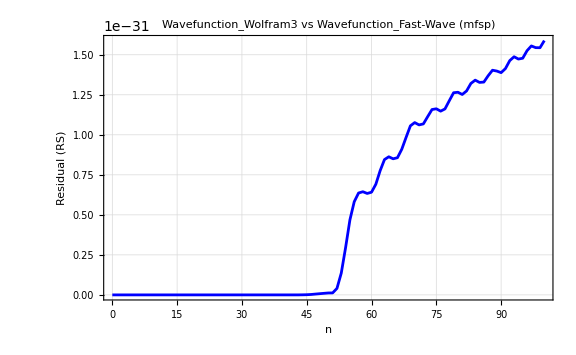

```mathematica
FastWaveMFSpN100x10=SetPrecision[Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_cython as wc;import numpy as np;N_max = 100;x2 =10.0;[wc.psi_n_multiple_fock_single_position(n,x2) for n in range(N_max+1)];"]],prec];

WavefunctionMFSpN100x10 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionMFSpN100x10 ,WavefunctionMathematica3[i-1,x2,prec]];]
ResidualList = (WavefunctionMFSpN100x10 - FastWaveMFSpN100x10)^2;

Residual = Mean /@ResidualList;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave (mfsp)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 10.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ]
```

#### Multiple Fock and Single Position Function with x = 20.0

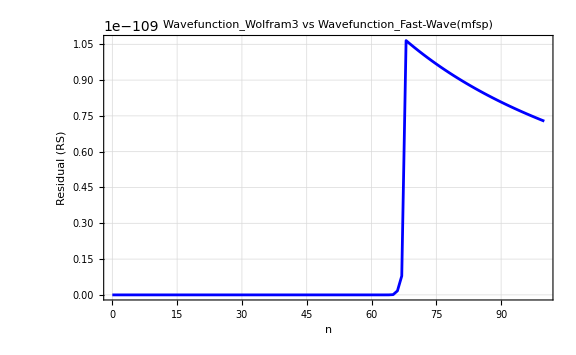

```mathematica
FastWaveMFSpN100x20=SetPrecision[Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_cython as wc;import numpy as np;N_max = 100;x3 =20.0;[wc.psi_n_multiple_fock_single_position(n,x3) for n in range(N_max+1)];"]],prec];

WavefunctionMFSpN100x20 = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WavefunctionMFSpN100x20 ,WavefunctionMathematica3[i-1,x3,prec]];]
ResidualList = (WavefunctionMFSpN100x20 - FastWaveMFSpN100x20)^2;

Residual = Mean /@ResidualList;

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mfsp)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" x: 20.0, to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ]
```

#### Multi Fock and Multiple Position Function with X = [(-20) → 20; 100]

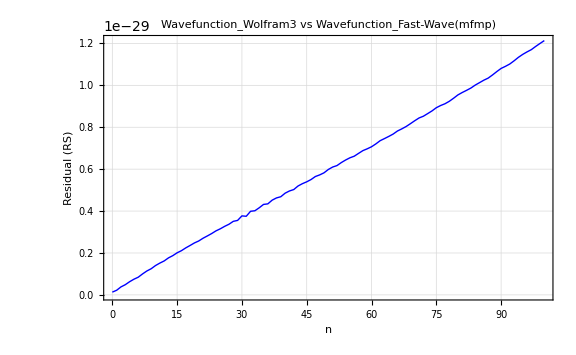

```mathematica
FastWaveMFMpN100X=SetPrecision[Normal[ExternalEvaluate["Python",                      "import fast_wave.wavefunction_cython as wc;import numpy as np;N_max = 100;xmax = 20.0;xmin=-20.0;xsize=100;X=np.linspace(xmin,xmax,xsize);[wc.psi_n_multiple_fock_multiple_position(n,X) for n in range(N_max+1)];"]],prec];

WolframMFMpN100X = {};
For[i=1,i<=(Nmax+1),i++,AppendTo[WolframMFMpN100X,WavefunctionMathematica3[i-1,Xvector,prec]];]

ResidualMatrixList = (WolframMFMpN100X - FastWaveMFMpN100X)^2;

Residual = Mean/@(Flatten/@ResidualMatrixList);

ListLinePlot[
Transpose[{Nvector,Residual}],
PlotStyle->{Thick,Blue},
Frame->True,
FrameLabel->{"n","Residual (RS)"},
PlotLabel->Style["Wavefunction_Wolfram3 vs Wavefunction_Fast-Wave(mfmp)\n",13,Bold],
GridLines->Automatic,
PlotLegends->Placed[{" X: [(-20)→20;100], to each value of n ; \n avg(RS) = [" <>ToString[SetPrecision[Mean[Residual],20],
TraditionalForm]} <> "]",Below],
ImageSize->Large ]
```